```mathematica
(* ===Import a BehaviorSpace Table-format CSV===*)ImportBehaviorSpace[csvPath_String,paramName_String,metricName_String]:=Module[{data,headerRow,columns,rows,records},data=Import[csvPath,"CSV"];
(*Find the column header row by locating "[run number]"*)headerRow=FirstPosition[data[[All,1]],"[run number]"][[1]];
columns=data[[headerRow]];
rows=Select[data[[headerRow+1;;]],Length[#]==Length[columns]&&#[[1]]=!=""&];
records=AssociationThread[columns,#]&/@rows;
(*Pull just the parameter and metric of interest*)Transpose[{#[paramName]&/@records,#[metricName]&/@records}]]
```

```mathematica
SetDirectory["/Users/brianbeckage/brianbeckage.github.io/teaching/EcologicalModeling/Solutions"]
```

/Users/brianbeckage/brianbeckage.github.io/teaching/EcologicalModeling/Solutions

```mathematica
Directory[]
```

/Users/brianbeckage/brianbeckage.github.io/teaching/EcologicalModeling/Solutions

```mathematica
FileNames[]
```

{Archived,Beckage_Netlogo7_butterfliesObs_sol.nlogox,Beckage_Netlogo7_butterfliesObs_sol q to maximize neighbors-spreadsheet.csv,Beckage_Netlogo7_butterfliesObs_sol q to maximize neighbors-table.csv,Beckage_Netlogo7_butterflies_sol.nlogox,Beckage_Netlogo7_mushroomHunter_sol.nlogox,Beckage_Stella_ClimateModel.stmx,Beckage_Stella_Collapse_p1.stmx,Beckage_Stella_Collapse_p2.stmx,Beckage_Stella_PopGrowth.stmx,Beckage_Stella_PopQ1_b_d.stmx,Beckage_Stella_PopQ2_K.stmx,Beckage_Stella_PopQ3_TimeDelay.stmx,Beckage_Stella_Predator_Prey.stmx,Beckage_wk10_butterflies_sol.nlogo,Beckage_wk10_butterflies_sol q to maximize neighbors-spreadsheet.csv,Corridor-output-for-q-0.2.csv,Corridor-output-for-q-0.7.csv,Corridor-output-for-q-1.csv,.DS_Store,examineBehaviorSpaceResults.nb,maxiNeighbors-spreadsheet.csv}

```mathematica
(* ===Use it===*)

points=ImportBehaviorSpace["Beckage_Netlogo7_butterfliesObs_sol q to maximize neighbors-table.csv","q","mean-Neighbors"];
```

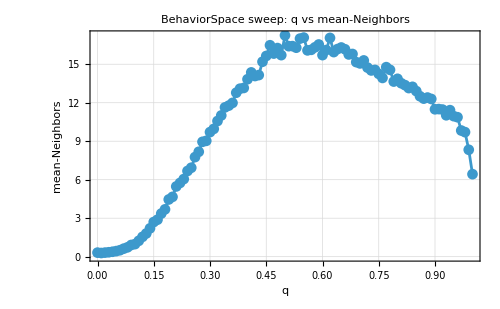

Best sampled q = 0.5  (mean-Neighbors = 17.2532)

Interpolated peak: q = 0.546114  (mean-Neighbors ≈ 17.1497)

```mathematica
(*If you have multiple reps per q value,average them*)
meanByQ=SortBy[KeyValueMap[{#1,Mean[#2]}&,GroupBy[points,First->Last]],First];


(* ===Plot the curve===*)

ListLinePlot[meanByQ,PlotMarkers->Automatic,Frame->True,FrameLabel->{"q","mean-Neighbors"},PlotLabel->"BehaviorSpace sweep: q vs mean-Neighbors",GridLines->Automatic,ImageSize->500]


(* ===Best q:simple argmax over the sampled points===*)

bestPoint=MaximalBy[meanByQ,Last][[1]];
Print["Best sampled q = ",bestPoint[[1]],"  (mean-Neighbors = ",bestPoint[[2]],")"]


(* ===Best q:interpolated peak (smoother estimate)===*)

interp=Interpolation[meanByQ,InterpolationOrder->3];
{peakValue,peakSol}=NMaximize[{interp[q],meanByQ[[1,1]]<=q<=meanByQ[[-1,1]]},q];
Print["Interpolated peak: q = ",q/. peakSol,"  (mean-Neighbors ≈ ",peakValue,")"]
```